## 1D+2D定态薛定谔方程

一维定态薛定谔方程

我们在坐标表象下进行定态方程的计算：

其中一维的势能设为：

-Graphics-

为了简便，我们设m=ℏ=ω=k=1，由此可以看一下势能在不同A下的大致图像：

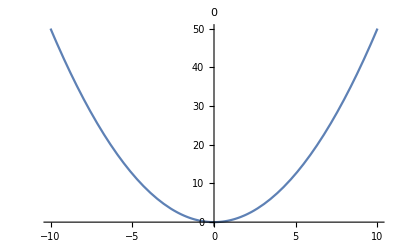
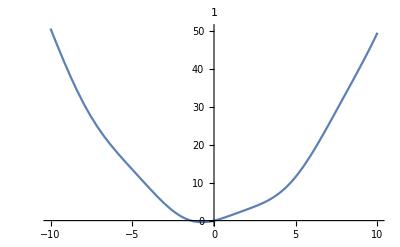
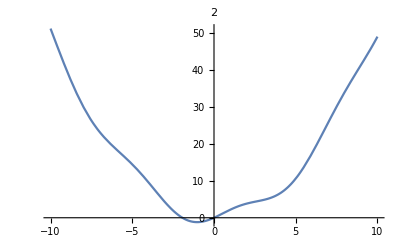
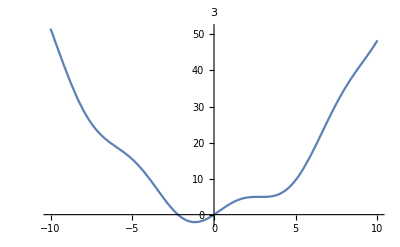
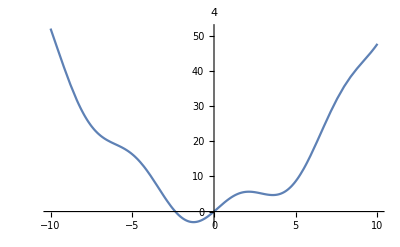
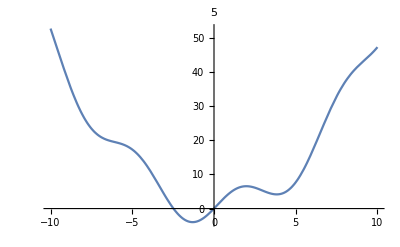

```mathematica
Table[Plot[1/2 x^2+a*Sin[x],{x,-10,10},PlotLabel->a],{a,0,5,1}]
```

之后进行动能和势能的离散化：-Graphics-
 (a)动能的离散化：
-Graphics-

 (b)势能的离散化：
 -Graphics-
 由此进行算符矩阵的构建。求得矩阵本征值和本征向量，从而得到本征能量和本征波函数。
 
 下面展示，从a取0到5间隔为1的能量本征值和波函数模方的结果(从左到右分别是势场V(x)、波函数和基态附近的能量本征值)：
 a=0
-Graphics--Graphics-
 
 
 a=1
-Graphics--Graphics-
 
 
 a=2
-Graphics--Graphics-


 a=3
-Graphics--Graphics-
 
 
 a=4
-Graphics--Graphics-
 
 
 a=5
-Graphics--Graphics-
 当a=0，即标准的谐振子，其本征能量有解析解即这里为(n+1/2)，可以看到计算结果完全符合这一结果，而且波函数模方的图样也符合厄密多项式，说明程序的正确性！
 当a逐渐增大，能量本征值逐渐减小，a=2时开始基态能量达到了负值，波函数也从刚开始的略微偏离厄密多项式，到完全偏离，基态开始出现双峰的结构。
 下面为对应的matlab代码：

```mathematica
=======matlab代码==============================
clear
clc

a = 0;
k = 1;
X = 10;     % 定义域:[-X,X] 
N = 200;    % 格点数 /in [-X,X]
dx = 2*X/N;   % 空间步长:定义域长度/格点数

x = linspace(-X,X,N);

% 势场
n = 2;      % 次数n
dxi = (2*X)/(N-1);
V = zeros([N,1]);
for xi = -X:dxi:X
V(round((xi+X)/dxi+1)) = 1/2*xi^n + a*sin(k*xi);  
end
A = spdiags(V,0,N,N);  % 提取V的对角线并生成势能矩阵
figure(1)
plot(V)

% 动能
H = zeros(N,3);
H(1:N,1) = -0.5/dx^2;
H(1:N,2) = 1/dx^2;
H(1:N,3) = -0.5/dx^2;
B = spdiags(H,-1:1,N,N);

C = A+B;
E = 9;    % 能级个数
% 求特征值
[Vector, Value] = eigs(C,E,0);  % 求指定的几个特征值

% 画图
for i = 1:E
    psi = Vector(:,i);
    figure(2)
    subplot(3,3,i)
    plot(x,abs(psi).^2/sum(abs(psi).^2*dx))
    ylim([0 0.8])
    xlabel('x');ylabel('P');
end

% 输出基态附近的能量值
v=[];
for i = 1:length(Value)
    v(i)= Value(i,i);
end
sort(v)

==============================================
```

二维定态薛定谔方程

与一维情况类似，我们采用离散的方法进行，只不过动能项略有变化：

-Graphics-
并且我们需要对二维的坐标进行一维化，即(i,j)对应 N(j-1)+i 的一维坐标，从而利用matlab当中的reshape函数进行。
为了验证程序的正确性，我们首先计算了二维谐振子的能量本征值(从左到右分别是势场V(x)、波函数和基态附近的能量本征值)：
-Graphics--Graphics--Graphics-
可以看到，本征能量近似为：1，2，2，3，3，3，4，4，4 ...； 这完全符合二维谐振子的本征能量：(1+nx+ny), 且具有相应的简并度！因此程序的正确性得以验证！


接下来，我们计算心形的势场：
-Graphics-
我们取a=0，1，2，3
a=0
-Graphics--Graphics--Graphics-


a=1
-Graphics--Graphics--Graphics-


a=2
-Graphics--Graphics--Graphics-


a=3   
-Graphics--Graphics--Graphics-
当a=0时，相当于没有势场，从而解出的是驻波；当a逐渐增大，可以看到基态能量不断下降，而且基态波函数局域在势场里面，并且逐渐变胖，这也符合a增大时，势场的区域增大的变化趋势。

下面为对应的matlab代码：

```mathematica
=======matlab代码==============================
clc
clear

a = 3;

% 最好设为偶数!
X = 10;     % 定义域:[-X,X]&[-X,X]
N = 100;    % 一维格点数 /in [-X,X]

% 空间步长:定义域长度/格点数
dx = 2*X/N;   
dy = dx;


% 势场
V = zeros([N,N]);
dxi = (2*X)/(N-1);
for xi = -X:dxi:X
    for yi = -X:dxi:X
    V(round((xi+X)/dxi+1),round((yi+X)/dxi+1)) = 1/2*(xi^2+yi^2);   %  二维谐振子

% if(xi*xi+yi*yi+a*xi-a*sqrt(xi*xi+yi*yi)<0)                        %  心形线势场
%       V(round((xi+X)/dxi+1),round((yi+X)/dxi+1)) = 0; 
% else
%      V(round((xi+X)/dxi+1),round((yi+X)/dxi+1)) = 8e4; 
% end

    end
end
VV = reshape(V',[N*N,1]);   % 转为一维对角元素
A = spdiags(VV,0,N*N,N*N);  % 提取V的对角线并生成势能矩阵

figure(1)
surf(V)


% 动能
H = zeros(N*N);
for j = 1 : N
    for i = 1 : N
        
     H(N*(j-1)+i,N*(j-1)+i) = -4;
     if(N*(j-1)+i+1>0 && N*(j-1)+i+1<N^2) % i+1
      H(N*(j-1)+i,N*(j-1)+i+1) = 1;
     end
     if(N*(j-1)+i-1>0 && N*(j-1)+i-1<N^2) % i-1
      H(N*(j-1)+i,N*(j-1)+i-1) = 1;
     end
      if(N*(j)+i>0 && N*(j)+i<N^2) % j+1
      H(N*(j-1)+i,N*(j)+i) = 1;
     end
     if(N*(j-2)+i>0 && N*(j-2)+i<N^2) % j-1
      H(N*(j-1)+i,N*(j-2)+i) = 1;
     end
      
    end
end

H = -1/(2*dx^2).*H;
B = sparse(H);

C = A+B;
E = 9;    % 能级个数
% 求特征值
[Vector, Value] = eigs(C,E,0);  % 求指定的几个特征值


% 画图
for i = 1:E
    psi = Vector(:,i);
    psi = reshape(psi,[N,N]);
    psi = abs(psi).^2/sum(sum(abs(psi).^2*dx*dx));
    figure(2)
    subplot(3,3,i)
    surf(psi)
end



% 输出基态附近的能量值
v=[];
for i = 1:length(Value)
    v(i)= Value(i,i);
end
sort(v)

==============================================
```